## NaCs 1Σ Hamiltonian, excluding hyperfine terms, including dipole-dipole interactions

## Description

This code simulates the dipolar interaction between two adjacent molecules. 

The full Hamiltonian of the molecules includes hyperfine states, which I ignore here. This assumption I am making is that if we initially populate a particular hyperfine state in N=0 with STIRAP (in our case, |I_Na=3/2, mI_Na=3/2, I_Cs=7/2, mI_Cs=5/2⟩ ), then we keep the same quantum numbers as we go to states with higher rotational quantum number N. This approximation is pretty good. At our large B-field of 860 G and large trap depth of several MHz, the nuclear spins and rotational angular momentum are almost fully uncoupled; the nuclear spins will point along the B field, and the rotational angular momentum will point along the tweezer AC electric field. 

By ignoring hyperfine quantum numbers, the single particle states are defined by|N, m_N⟩ . I define a single particle and two particle Hilbert space, and single particle and two particle Hamiltonians. Since all Hamiltonians are time-independent, I compute unitary evolution using the matrix exponent function.

## Setup

### Helper functions

```mathematica
kp[a_,b_]:=KroneckerProduct[a,b](*shorthand Kronecker product*)
conj=Complex[a_,b_]->Complex[a,-b];(*shorthand complex conjugate*)
{αpar,αperp,α0,Δ,B,U,Int,d,r,ϵ0,h}=.;
```

### Constants and units

#### Definition

Specifying all constants. The tunable parameters are in the ‘experiment’ association.

```mathematica
units=Association[cm->Quantity[1,"Centimeters"],um->Quantity[1,"Micrometers"],nm->Quantity[1,"Nanometers"],Hz->Quantity[1,"Hertz"],kHz->Quantity[1,"Kilohertz"],MHz->Quantity[1,"Megahertz"],GHz->Quantity[1,"Gigahertz"],THz->Quantity[1,"Terahertz"],icm->Quantity[1,("Centimeters")^-1],Debye->Quantity[1,"Debyes"],Gauss->Quantity[1,"Gauss"],mV->Quantity[1,"Millivolts"],V->Quantity[1,"Volts"]];
fundamental=Association[ϵ0->Quantity["Permittivity of free space"],ℏ->Quantity["ReducedPlanckConstant"],h->Quantity["PlanckConstant"],μB->Quantity["BohrMagneton"],μN->Quantity["NuclearMagneton"],a0->Quantity[1,"BohrRadius"]];
polarizability=Association[αpar->1872.12,αperp->467.038,Δ->αpar-αperp,α0->(αpar+2αperp)/3]/.units/.fundamental;
nacs=Association[I1->3/2,I2->7/2,Bv->h 1.7396 GHz,eQq1->-h 97 kHz,eQq2->h 150 kHz,c1->h 14.2 Hz,c2->h 854.5 Hz,c3->h 105.6 Hz,c4->h 3941.8 Hz,gr->0,g1->1.478,g2->0.738,σ1->0.0006392,σ2->0.0062787,d0->4.6 Debye]/.units/.fundamental;
krb=Association[Bv->h 1.11395 GHz,eQq1->h 450 kHz,eQq2->-h 1.41 MHz,c1->-h 24.1 Hz,c2->h 420.1 Hz,c3->h 0 Hz,c4->-h 2030.4 Hz,gr->0,g1->-0.324,g2->1.834,σ1->1321 10^-6,σ2->3469 10^-6,d0->1 Debye]/.units/.fundamental;
experiment=Association[r->2.6 um,θh->(π-ArcCos[1/√3])/2,θq->π/2-ArcCos[1/√3],U->h 10 MHz,B0->860 Gauss,E0->10^-8 mV/cm,θB->0,ϕB->0,θE->0,ϕE->0]/.units/.fundamental;
```

#### Default values

Defining which constants are used in the code below.

```mathematica
molecule=nacs;
constants=Association[{units,fundamental,polarizability,molecule,experiment}];
```

### Hilbert space

Defines the single particle and multi-particle Hilbert spaces. For each state in the Hilbert space, there is an associated label with its quantum numbers.

#### Single particle

```mathematica
nM=2; (*maximum rotational angular momentum N*)
nℋ1=Sum[2N+1,{N,0,nM}]; (*number of states in the Hilbert space*)
nP=2;(*number of particles that interact (only works for 2 particles for now*)

ℋ1=IdentityMatrix[nℋ1];(*Single particle Hilbert space.*)
sℋ1=Partition[ℋ1,{nℋ1,1}][[1]];(*States in the single particle Hilbert space. These are column vectors with a single 1.*)
lℋ1=Flatten[Table[{n,m},{n,0,nM},{m,-n,n}],1];(*List of state labels. These are strings of|N,m⟩ for all possible values of N and m*)
yℋ1=Flatten[Table[SphericalHarmonicY[n,m,θ,ϕ],{n,0,nM},{m,-n,n}],1];(*List of spherical harmonics Subscript[Y, n,m] for all possible values of N and m*)
s2lℋ1=AssociationThread[sℋ1->lℋ1] (*Association between states and labels*);
l2sℋ1=AssociationThread[lℋ1->sℋ1]; 
l2yℋ1=AssociationThread[lℋ1->yℋ1]; 
y2lℋ1=AssociationThread[yℋ1->lℋ1];
```

#### Multi-particle

```mathematica
ℋn=IdentityMatrix[nℋ1^nP];(*multi-particle Hilbert space*)
nℋn=Length[ℋn];(*number of states in the multi-particle Hilbert space*)
sℋn=Partition[ℋn,{nℋ1^nP,1}][[1]];(*states in the multi-particle Hilbert space*)
lℋn=Flatten[Table[{{ni,mi},{nj,mj}},{ni,0,nM},{mi,-ni,ni},{nj,0,nM},{mj,-nj,nj}],3];(*multi-particle state labels |Subscript[N, i],Subscript[m, i]⟩|Subscript[N, j],Subscript[m, j]⟩*)
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
```

### Polarization

#### Jones matrices

Defines the tweezer polarization seen by the molecule, and calculates the angle between the quantization axis and the array.

```mathematica
{θ,ϕ,θd}=.;
qwp[θ_]=Exp[-(ⅈ π)/4]({{Cos[θ]^2+ⅈ Sin[θ]^2, (1-ⅈ) Sin[θ]Cos[θ]}, {(1-ⅈ) Sin[θ]Cos[θ], Sin[θ]^2+ⅈ Cos[θ]^2}});(*quarter waveplate Jones matrix*)
hwp[θ_]=Exp[-(ⅈ π)/2]({{Cos[θ]^2-Sin[θ]^2, 2Cos[θ]Sin[θ]}, {2Cos[θ]Sin[θ], Sin[θ]^2-Cos[θ]^2}});(*half waveplate Jones matrix*)
lpr[η_,θ_]=Exp[-(ⅈ η)/2]({{Cos[θ]^2+Exp[ⅈ η] Sin[θ]^2, (1-Exp[ⅈ η])Cos[θ]Sin[θ]}, {(1-Exp[ⅈ η])Cos[θ]Sin[θ], Sin[θ]^2+Exp[ⅈ η] Cos[θ]^2}});(*linear phase retarder Jones matrix*)

jH=({{1}, {0}});jV=({{0}, {1}});jL=1/(√2)({{1}, {ⅈ}});jR=1/(√2)({{1}, {-ⅈ}});(*Jones vectors for horizontal, vertical, LCP, and RCP light*)
jF[θh_,θq_]=FullSimplify[Flatten[hwp[θh].qwp[θq].jH],Assumptions->{0<=θh<2π,0<=θq<2π}];(*Jones vector seen by molecules*)

pEllipse[θh_,θq_]=FullSimplify[ComplexExpand[Re[jF[θh,θq]Exp[-ⅈ t]]],Assumptions->{t>0,0<=θh<2π,0<=θq<2π}];(*Visualization of the polarization ellipse*)
θd[θh_,θq_]:=ArcCos[Sin[2θh-θq]](*Angle between minor axis and array*)
```

#### Polarizability

Defining the AC Stark shift of a molecule in an off-resonant AC electric field (caused by the tweezer). I express the molecular frame polarizability in the lab frame by rotating the molecular frame matrix by θ and ϕ. I multiply the lab frame polarizability on both sides by the AC electric field, which gives the tweezer induced potential energy of the molecule as a function of orientation (θ,ϕ). Conceptually, the potential will be lower when the angles θ and ϕ are chosen to make the internuclear axis align with the electric field. To find the differential AC Stark shift relative to the ground state, I subtract the potential energy of the ground state, which, by having an isotropic polarizability, is independent of θ and ϕ. This differential potential energy is the term β in the code below.

```mathematica
{ϵ,n1,m1,n2,m2}=.;
αM=({{αperp, 0, 0}, {0, αperp, 0}, {0, 0, αpar}});(*Polarizability tensor in the molecular frame. It is diagonal for a linear molecule*)
Rx=RotationMatrix[θ,{1,0,0}];
Ry=RotationMatrix[θ,{0,1,0}];
Rz=RotationMatrix[ϕ,{0,0,1}];
ϵ[θh_,θq_]={Append[jF[θh,θq],0]}ᵀ;(*Jones vector seen by the molecule, expressed in 3D coordinates*)
αL=Rzᵀ.Ryᵀ.αM.Ry.Rz;
β[θ_,ϕ_]=-U/α0((ϵ[θh,θq]ᵀ/.Complex[a_,b_]->Complex[a,-b]).αL.ϵ[θh,θq]-(αpar+2αperp)/3//FullSimplify)[[1,1]]/.(αpar-αperp)->Δ;(*Differential light shift relative to N=0. The rotation matrices express the polarizability tensor in the lab frame.*)
```

### Dipole-dipole interaction

The transition dipole moment between two states differing by angular momentum q  is given by dpME, taken from Wall et. al. The dipole dipole Hamiltonian induces correlated transitions between two molecules. These correlated transitions can be seen by the dipole-dipole matrix elements.

```mathematica
dpME[q_,{Nb_,mb_},{Nk_,mk_}]:=Quiet[(-1)^mb √((2 Nb+1) (2 Nk+1)) ThreeJSymbol[{Nb,-mb},{1,q},{Nk,mk}] ThreeJSymbol[{Nb,0},{1,0},{Nk,0}]](*dipole matrix element for spherical component q between bra Nm and ket Nm*)
HddME[{b1_,b2_},{k1_,k2_}]:=dpME[0,b1,k1]dpME[0,b2,k2]+(dpME[1,b1,k1]dpME[-1,b2,k2]+dpME[-1,b1,k1]dpME[1,b2,k2])/2
```

### Selection rules

The AC Stark shift only couples states whose N and mN differ by 0 or 2. Note that below I am only letting interactions occur between same N states, which is an approximation. The dipole dipole interaction only couples states that are exchanging states that are one N apart. Defining selection rules greatly speeds up the computation of the AC and DD Hamiltonians.

```mathematica
srAC[{n1_,m1_},{n2_,m2_}]:=(n1==n2)∧(m1==m2∨Abs[m1-m2]==2)
srDD[{{bn1_,bm1_},{bn2_,bm2_}},{{kn1_,km1_},{kn2_,km2_}}]:={bn1,bm1}=={kn2,km2}∧{bn2,bm2}=={kn1,km1}∧Abs[bn1-bn2]==1
```

### Hamiltonians

#### Single particle

```mathematica
H0ℋ1=SparseArray[{i_,i_}->2Bv lℋ1[[i,1]],{nℋ1,nℋ1}]//Quiet;(*Rotation Hamiltonian*) (*CORRECT*)
```

```mathematica
Hacℋ1=SparseArray[ParallelTable[If[srAC[lℋ1[[i]],lℋ1[[j]]],Integrate[(yℋ1[[i]]/.conj)yℋ1[[j]]β[θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π},Assumptions->{θh>0,θq>0,Δ>0}],0],{i,1,nℋ1},{j,1,nℋ1}]];(*Tweezer AC-electric field Hamiltonian*)
```

```mathematica
(*Ω={Ωm,Ω0,Ωp};
HΩℋ1=Sum[Ω[[q+2]]l2sℋ1[{0,0}].l2sℋ1[{1,q}]ᵀ,{q,-1,1}]+Sum[Ω[[q+2]]l2sℋ1[{0,0}].l2sℋ1[{1,q}]ᵀ,{q,-1,1}]ᵀ+Sum[-ΔΩ l2sℋ1[{1,q}].l2sℋ1[{1,q}]ᵀ,{q,-1,1}];*)
Hℋ1=H0ℋ1+Hacℋ1;
```

#### Multi-particle

```mathematica
H1ℋn=kp[Hℋ1,ℋ1]+kp[ℋ1,Hℋ1];
Hddℋn=d0^2(1-3 Cos[θ]^2)/(4π ϵ0 r^3)SparseArray[{i_,j_}/;srDD[lℋn[[i]],lℋn[[j]]]->HddME[lℋn[[i]],lℋn[[j]]],{nℋn,nℋn}]//Quiet;
Hℋn=H1ℋn+Hddℋn;
```

#### Eigenvalues

```mathematica
{evalsAC,evecsAC}=Eigensystem[Hacℋ1]//FullSimplify;
```

## Results

### Find AC eigenstates

```mathematica
evecsACn={(Normalize/@(evecsAC/.constants//N//Chop))[[#]]}ᵀ&/@Range[nℋ1];
evalsACn=Chop[QuantityMagnitude[UnitConvert[evalsAC/h//.constants]],10^-9];
```

### Dipolar interaction

Interaction from 0_i 1_jto 1_i 0_j, where i and j are sites and 0 and 1 represent N=0 and N=1 states:

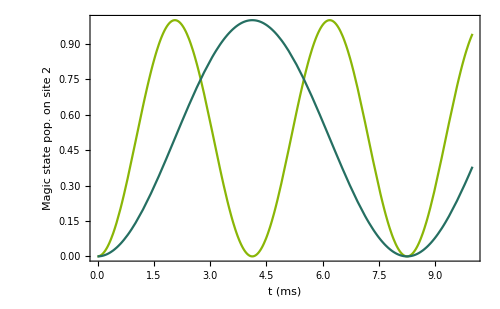

```mathematica
Hn=Chop[QuantityMagnitude[UnitConvert[Normal[Hℋn]/h//.r->2.6um/.θ->θd[θh,θq]//.constants]],10^-9];
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black]; 
Plot[Evaluate@(Abs[kp[sℋ1[[1]],evecsACn[[#]]]ᵀ.Quiet[MatrixExp[-ⅈ 2π t 10^-3 Hn]].kp[evecsACn[[#]],sℋ1[[1]]]]^2&/@{3,5}),{t,0,10 },FrameLabel->{"t (ms)","Magic state pop. on site 2"},PlotStyle->{ColorData[3,4],ColorData[3,5]}]
```

```mathematica
tπ = 22.3 us
t_total=500 us
```